# Title

Author Name

Abstract

## Section

XXXX:

## API

```mathematica
api=APIFunction["city"->"City",WeatherData[#city,"Temperature"]&];
```

```mathematica
weatherreport=CloudDeploy[api,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/d9b2ef0d-5c9c-482c-a2ce-82a6783fa0e0]

```mathematica
URLExecute[weatherreport,{"city"->"London"}]
```

17 °C

```mathematica
URLExecute[weatherreport,{"city"->"New York City"}]
```

12.8 °C

```mathematica
URLExecute[weatherreport,{"city"->"Beijing"}]
```

8.99999 °C

```mathematica
URLExecute[weatherreport,{"city"->"Paris"}]
```

13 °C

```mathematica
URLExecute[weatherreport,{"city"->"Jerusalem"}]
```

30 °C

```mathematica
URLExecute[weatherreport,{"city"->"Prague"}]
```

7.99999 °C

```mathematica
URLExecute[weatherreport,{"city"->"Minsk"}]
```

6.99999 °C

```mathematica
URLExecute[weatherreport,{"city"->"Tokyo"}]
```

24 °C

```mathematica
CloudDeploy[APIFunction["city"->"City",WeatherData[
#city,"Temperature"]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/22f85710-791c-4e69-9406-c26b21f31136]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,WeatherData[#city,"Temperature"]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/764e2525-4330-4972-b6ef-b2f620cf86e8]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{#city["Name"]},{"Current Temperature",WeatherData[#city,"Temperature"]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/2ba671ed-97a2-43f3-bd10-25614073ea7a]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/24cdeecf-0ae1-46d8-b7e7-2c49c547ab10]

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Relative Humidity","Subsubsection"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]],QuantityForm[WeatherData[#city,"Humidity"],"Abbreviation"]},{Style["Current Wind Speed","Subsubsection"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Wind Direction","Subsubsection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]],QuantityForm[WeatherData[#city,"WindDirection"],"Abbreviation"]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/41ef85f9-dbcd-47b3-bb43-c2943abd7097]

```mathematica
?IconData
```

```mathematica
WeatherData[Here,"Humidity"]
```

0.404

```mathematica
WeatherData[Here,"WindSpeed"]
```

5.4 km/h

```mathematica
WeatherData[Here,"WindDirection"]
```

330 °

```mathematica
MoonPhase["SignedFraction"]
```

0.7265

```mathematica
MoonPhase["Icon"]
```

-Graphics-

```mathematica
MoonPhase["Name"]["Name"]
```

waxing gibbous moon

```mathematica
CanonicalName[MoonPhase["Name"]]
```

WaxingGibbous

```mathematica
URLExecute[CloudObject[["https://www.wolframcloud.com/obj/41ef85f9-dbcd-47b3-bb43-c2943abd7097"](https://www.wolframcloud.com/obj/41ef85f9-dbcd-47b3-bb43-c2943abd7097)],{"city"->"Tokyo"}]
```

I think there's nothing because I have the option CloudCDF enabled.

```mathematica
CloudDeploy[APIFunction["city"->"City"->$GeoLocationCity,Grid[{{Style[#city["Name"],"Title"]},{Style["Current Temperature","Subsubsection"],IconData["AirTemperature",WeatherData[#city,"Temperature"]],QuantityForm[WeatherData[#city,"Temperature"],"Abbreviation"]},{Style["Current Relative Humidity","Subsubsection"],IconData["RelativeHumidity",WeatherData[#city,"Humidity"]],QuantityForm[WeatherData[#city,"Humidity"],"Abbreviation"]},{Style["Current Wind Speed","Subsubsection"],IconData["WindSpeed",WeatherData[#city,"WindSpeed"]],QuantityForm[WeatherData[#city,"WindSpeed"],"Abbreviation"]},{Style["Current Wind Direction","Subsubsection"],IconData["WindDirection",WeatherData[#city,"WindDirection"]],QuantityForm[WeatherData[#city,"WindDirection"],"Abbreviation"]},{Style["Geographical position","Subsubsection"],FromDMS[EntityValue[#city,"Position"]],DMSString[EntityValue[#city,"Position"]]},{Style["Current time","Subsubsection"],DateString[Now,"DateTime"]},{Style["Geographical xyz position","Subsubsection"],Floor[First[GeoPositionXYZ[EntityValue[#city,"Position"]]]]},{Style["Geographical projected position with Bonne grid projection","Subsubsection"],First[GeoGridPosition[EntityValue[#city,"Position"],"Bonne"]]},{Style["Geographical projected position with Mercator grid projection","Subsubsection"],First[GeoGridPosition[EntityValue[#city,"Position"],"Mercator"]]},{Style["Geographical position with New York City as the center","Subsubsection"],First[GeoPositionENU[EntityValue[#city,"Position"],EntityValue[Entity["City",{"NewYork","NewYork","UnitedStates"}],"Position"]]]},{Style["Geographical antipode and elevation","Subsubsection"],First[GeoPosition[GeoAntipode[EntityValue[#city,"Position"]]]],QuantityForm[UnitConvert[GeoElevationData[First[GeoPosition[GeoAntipode[EntityValue[#city,"Position"]]]]],"SIBase"],"Abbreviation"]},{Style["Geographical elevation","Subsubsection"],QuantityForm[UnitConvert[GeoElevationData[EntityValue[#city,"Position"]],"SIBase"],"Abbreviation"]},
{Style["Gravity magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Gravity north component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity east component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity down component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Gravity declination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Gravity inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Gravity potential data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Magnetic magnitude data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Magnitude"],"SIBase"],"Abbreviation"]},{Style["Magnetic north component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"NorthComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic east component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"EastComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic down component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"DownComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic horizontal component data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"HorizontalComponent"],"SIBase"],"Abbreviation"]},{Style["Magnetic declination data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Declination"],"SIBase"],"Abbreviation"]},{Style["Magnetic inclination data","Subsubsection"],QuantityForm[UnitConvert[GeogravityModelData[EntityValue[#city,"Position"],"Inclination"],"SIBase"],"Abbreviation"]},{Style["Magnetic potential data","Subsubsection"],QuantityForm[UnitConvert[GeomagneticModelData[EntityValue[#city,"Position"],"Potential"],"SIBase"],"Abbreviation"]},{Style["Cloud Cover Fraction Data","Subsubsection"],WeatherData[EntityValue[#city,"Position"],"CloudCoverFraction"]},{Style["Dew Point Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"DewPoint"],"SI"],"Abbreviation"]},{Style["Pressure Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"Pressure"],"SI"],"Abbreviation"]},{Style["Visibility Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"Visibility"],"SI"],"Abbreviation"]},{Style["Wind Chill Data","Subsubsection"],QuantityForm[UnitConvert[WeatherData[EntityValue[#city,"Position"],"WindChill"],"SI"],"Abbreviation"]},{Style["Moon Position True Equatorial Altitude","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"]},{Style["Moon Equatorial Position Altitude with atmospheric refraction taken into account","Subsubsection"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]},{Style["Moon Position True Altitude Horizon System","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"]},{Style["Moon Position Altitude with Horizon System with atmospheric refraction taken into account","Subsubsection"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]}},Alignment->Left]&,"CloudCDF"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/7a4c7402-950a-4ef7-902b-631fd7872684]

```mathematica
GeogravityModelData[Here]
```

<|Magnitude→9.79953 m/s^2,NorthComponent→0.0000186985 m/s^2,EastComponent→0.000080347 m/s^2,DownComponent→9.79953 m/s^2,HorizontalComponent→0.0000824941 m/s^2,Declination→76.8992 °,Inclination→89.9995 °,Potential→-6.26348×10^7 J/kg|>

```mathematica
GeomagneticModelData[Here]
```

<|Magnitude→51057.1 nT,NorthComponent→20949.7 nT,EastComponent→-2693.28 nT,DownComponent→46483.2 nT,HorizontalComponent→21122.1 nT,Declination→-7.32574 °,Inclination→65.5628 °,Potential→-1.40253×10^8 s nV/m|>

```mathematica
DMSString[Here]
```

38°24'36.000"N 82°26'24.000"W

```mathematica
FromDMS["38°24'36.000\"N 82°26'24.000\"W"]
```

{38.41,-82.44}

```mathematica
GeoPositionXYZ[Here]
```

GeoPositionXYZ[{658385.,-4.96078×10^6,3.94121×10^6}]

```mathematica
First[GeoPositionXYZ[Here]]
```

{658385.,-4.96078×10^6,3.94121×10^6}

```mathematica
Floor[First[GeoPositionXYZ[Here]]]
```

{658385,-4960784,3941205}

```mathematica
GeoGridPosition[Here,"Bonne"]
```

GeoGridPosition[{-0.973572,1.15548},Bonne]

```mathematica
First[GeoGridPosition[Here,"Bonne"]]
```

{-0.973572,1.15548}

```mathematica
GeoPositionENU[Here,GeoPosition["NorthPole"]]
```

GeoPositionENU[{-4.96078×10^6,-658385.,-2.41555×10^6},GeoPosition[{90,0}]]

```mathematica
GeoPositionENU[Here,EntityValue[,"Position"]]
```

GeoPositionENU[{-739810.,-214387.,-46632.6},GeoPosition[{40.6643,-73.9385}]]

```mathematica
First[GeoPositionENU[Here,EntityValue[,"Position"]]]
```

{-739810.,-214387.,-46632.6}

```mathematica
First[GeoPositionENU[,EntityValue[,"Position"]]]
```

{0.,0.,0.}

```mathematica
First[GeoAntipode[Here]]
```

{-38.41,97.56}

```mathematica
GeoElevationData[First[GeoAntipode[Here]]]
```

-4139. m

```mathematica
GeogravityModelData[Here]
```

<|Magnitude→9.79953 m/s^2,NorthComponent→0.0000186985 m/s^2,EastComponent→0.000080347 m/s^2,DownComponent→9.79953 m/s^2,HorizontalComponent→0.0000824941 m/s^2,Declination→76.8992 °,Inclination→89.9995 °,Potential→-6.26348×10^7 J/kg|>

```mathematica
GeogravityModelData[Here,"Magnitude"]
```

9.79952 m/s^2

```mathematica
WeatherData[$GeoLocationCity,{"CloudCoverFraction","CloudHeight","CloudTypes"}]
```

WeatherData[{Huntington,WestVirginia,UnitedStates},{CloudCoverFraction,CloudHeight,CloudTypes}]

```mathematica
WeatherData[$GeoLocationCity,"CloudCoverFraction"]
```

0

```mathematica
WeatherData[$GeoLocationCity,"CloudHeight"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"CloudTypes"]
```

{}

```mathematica
WeatherData[$GeoLocationCity,"DewPoint"]
```

3.89999 °C

```mathematica
WeatherData[$GeoLocationCity,"PrecipitationRate"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"Pressure"]
```

1020.1 mbar

```mathematica
WeatherData[$GeoLocationCity,"StationPressure"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"Visibility"]
```

16.09 km

```mathematica
WeatherData[$GeoLocationCity,"WindDirection"]
```

0 °

```mathematica
WeatherData[$GeoLocationCity,"WindChill"]
```

20.71 °C

```mathematica
WeatherData[$GeoLocationCity,"WindGusts"]
```

Missing[NotAvailable]

```mathematica
WeatherData[$GeoLocationCity,"WindSpeed"]
```

0 km/h

```mathematica
WeatherData[$GeoLocationCity,"MeanHumidity"]
```

Missing[NotApplicable]

```mathematica
WeatherData[$GeoLocationCity,"Coordinates"]
```

{38.365,-82.555}

```mathematica
WeatherData[$GeoLocationCity,"CloudCoverFraction",{Today-Quantity[3, "Weeks"],Today}]
```

TimeSeries[…]

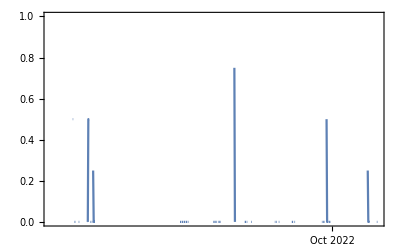

```mathematica
DateListPlot[%117]
```

```mathematica
MoonPosition[]
```

{192.41 °,26.82 °}

```mathematica
MoonPosition[CelestialSystem->"Horizon"]
```

{340.8 °,-72. °}

```mathematica
MoonPosition[CelestialSystem->"Equatorial"]
```

{21.345 ^h,-21.238 °}

```mathematica
MoonPosition[]
```

{340.93 °,-72.01 °}

```mathematica
{MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"TrueAltitude"],MoonPosition[CelestialSystem->"Equatorial",AltitudeMethod->"ApparentAltitude"]}
```

{{21.346 ^h,-21.235 °},{21.346 ^h,-21.235 °}}

```mathematica
{MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"TrueAltitude"],MoonPosition[CelestialSystem->"Horizon",AltitudeMethod->"ApparentAltitude"]}
```

{{341.66 °,-72.07 °},{341.66 °,-72.08 °}}